Underdamped 1

```mathematica
$Assumptions={τ>0,γ>0,ω0>0,√(ω0^2-γ^2/4)>0,τ>=t>=0,τ>=u>=0,n∈Integers};
```

```mathematica
(* Relaxation function and derivatives *)
```

```mathematica
Psi[t_]=Exp[-γ/2 Abs[t]](Cos[√(ω0^2-γ^2/4)t]+γ/(2 √(ω0^2-γ^2/4))Sin[√(ω0^2-γ^2/4)Abs[t]]);
dPsi[t_]=-(2 ⅇ^(-1/2 γ Abs[t]) ω0^2 Sin[t √(-γ^2/4+ω0^2)])/(√(-γ^2+4 ω0^2));
ddPsi[t_]=-ⅇ^(-1/2 γ Abs[t]) ω0^2 Cos[t √(-γ^2/4+ω0^2)]+(ⅇ^(-1/2 γ Abs[t]) γ ω0^2 Sin[Abs[t] √(-γ^2/4+ω0^2)])/(√(-γ^2+4 ω0^2));
```

```mathematica
(* Dirac delta coefficients *)
```

```mathematica
f[s_]=-1/(s LaplaceTransform[ddPsi[t],t,s]);

c0=SeriesCoefficient[f[s],{s,0,0}];

c1=SeriesCoefficient[f[s],{s,0,1}];

c2=SeriesCoefficient[f[s],{s,0,2}];
```

```mathematica
(* Parameters and protocols *)
```

```mathematica
γ=1;
ω0=1;
τR=γ/ω0^2;
g[t_]=(t+τR)/(τ+2τR);
h1[t_]=t/τ;
dh1[t_]=h1'[t];
h2[t_]=(t/τ)^2;
dh2[t_]=h2'[t];
h3[t_]=(t/τ)^3;
dh3[t_]=h3'[t];
```

```mathematica
(* Calculation of the irreversible works *)
```

```mathematica
W0[τ_]=Psi[0]/2+Integrate[dPsi[τ-t]g[t],{t,0,τ}]-1/2 Integrate[ddPsi[t-u]g[t]g[u],{t,0,τ},{u,0,τ}]
```

1/2-(ⅇ^(-τ/2) (3 ⅇ^(τ/2) τ-2 √3 Sin[(√3 τ)/2]))/(3 (2+τ))+(ⅇ^(-τ/2) (6 ⅇ^(τ/2)+6 ⅇ^(τ/2) τ+3 ⅇ^(τ/2) τ^2-6 Cos[(√3 τ)/2]-6 √3 Sin[(√3 τ)/2]-4 √3 τ Sin[(√3 τ)/2]))/(6 (2+τ)^2)

```mathematica
W1[τ_]=Psi[0]/2+1/2 Integrate[dPsi[τ-t]g[t],{t,0,τ}]+(c0(dPsi[τ]-dPsi[0]))/(2(τ+2τR))
```

1/2-(ⅇ^(-Abs[τ]/2) Sin[(√3 τ)/2])/(√3 (2+τ))-(ⅇ^(-τ/2) (3 ⅇ^(τ/2) τ-2 √3 Sin[(√3 τ)/2]))/(6 (2+τ))

```mathematica
Wh1[τ_]=1/2 Integrate[Psi[t-u]dh1[t]dh1[u],{t,0,τ},{u,0,τ}]
```

(ⅇ^(-τ/2) (3 ⅇ^(τ/2) τ-2 √3 Sin[(√3 τ)/2]))/(3 τ^2)

```mathematica
Wh2[τ_]=1/2 Integrate[Psi[t-u]dh2[t]dh2[u],{t,0,τ},{u,0,τ}]
```

(4 ⅇ^(-τ/2) (-3 ⅇ^(τ/2)+ⅇ^(τ/2) τ^3+3 Cos[(√3 τ)/2]+3 τ Cos[(√3 τ)/2]-√3 Sin[(√3 τ)/2]+√3 τ Sin[(√3 τ)/2]))/(3 τ^4)

```mathematica
Wh3[τ_]=1/2 Integrate[Psi[t-u]dh3[t]dh3[u],{t,0,τ},{u,0,τ}]
```

1/(5 τ^6)3 ⅇ^(-τ/2) (-60 ⅇ^(τ/2)-10 ⅇ^(τ/2) τ^3+3 ⅇ^(τ/2) τ^5+60 Cos[(√3 τ)/2]-30 τ^2 Cos[(√3 τ)/2]+20 √3 Sin[(√3 τ)/2]+40 √3 τ Sin[(√3 τ)/2]+10 √3 τ^2 Sin[(√3 τ)/2])

```mathematica
(* Irreversible works *)
```

```mathematica
W1[τ_]=1/2-(ⅇ^(-Abs[τ]/2) Sin[(√3 τ)/2])/(√3 (2+τ))-(ⅇ^(-τ/2) (3 ⅇ^(τ/2) τ-2 √3 Sin[(√3 τ)/2]))/(6 (2+τ));
W0[τ_]=1/2-(ⅇ^(-τ/2) (3 ⅇ^(τ/2) τ-2 √3 Sin[(√3 τ)/2]))/(3 (2+τ))+(ⅇ^(-τ/2) (6 ⅇ^(τ/2)+6 ⅇ^(τ/2) τ+3 ⅇ^(τ/2) τ^2-6 Cos[(√3 τ)/2]-6 √3 Sin[(√3 τ)/2]-4 √3 τ Sin[(√3 τ)/2]))/(6 (2+τ)^2);
Wh1[τ_]=(ⅇ^(-τ/2) (3 ⅇ^(τ/2) τ-2 √3 Sin[(√3 τ)/2]))/(3 τ^2);
Wh2[τ_]=(4 ⅇ^(-τ/2) (-3 ⅇ^(τ/2)+ⅇ^(τ/2) τ^3+3 Cos[(√3 τ)/2]+3 τ Cos[(√3 τ)/2]-√3 Sin[(√3 τ)/2]+√3 τ Sin[(√3 τ)/2]))/(3 τ^4);
Wh3[τ_]=1/(5 τ^6)3 ⅇ^(-τ/2) (-60 ⅇ^(τ/2)-10 ⅇ^(τ/2) τ^3+3 ⅇ^(τ/2) τ^5+60 Cos[(√3 τ)/2]-30 τ^2 Cos[(√3 τ)/2]+20 √3 Sin[(√3 τ)/2]+40 √3 τ Sin[(√3 τ)/2]+10 √3 τ^2 Sin[(√3 τ)/2]);
```

```mathematica
(* Plots *)
```

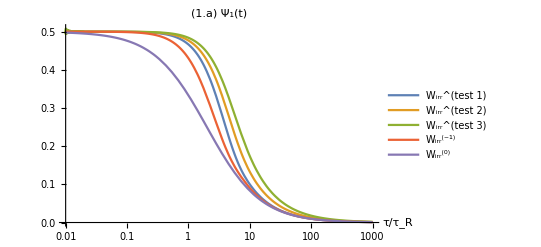

```mathematica
LogLinearPlot[{Legended[Wh1[τ],"W_irr^(test 1)"],Legended[Wh2[τ],"W_irr^(test 2)"],Legended[Wh3[τ],"W_irr^(test 3)"],Legended[W0[τ],"W_irr^(-1)"],Legended[W1[τ],"W_irr^(0)"]},{τ,0.01,1000},PlotRange->Full,AxesLabel->{"τ/τ_R"},PlotLegends->Placed[{},{Right,Center}],PlotLabel->"(1.a) Ψ_1(t)"]
Clear[τR,γ,ω0]
```

```mathematica
(* Error *)
```

```mathematica
ϵ1[τ_]= Abs[(W1[τ]-W0[τ])/W1[τ]];
```

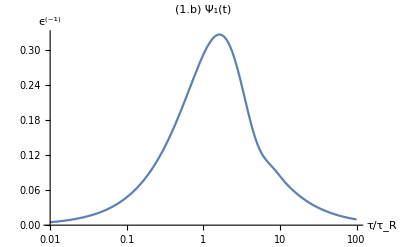

```mathematica
LogLinearPlot[ϵ1[τ],{τ,0.01,100},PlotRange->Full,AxesLabel->{"τ/τ_R","ϵ^(-1)"},PlotLabel->"(1.b) Ψ_1(t)"]
```